# Introduction to Stochastic Processes

Collections of random variables are useful models of many random processes

Colin Nancarrow, Jun. 24,  2018

A stochastic process is a collection of random variables indexed by some set. For example, a random variable is the simplest kind of stochastic process: it’s just a random variable indexed by one object, or the singleton set. The most common sets used to index random variables in stochastic processes are:
	1. The singleton set for a single random variable 
	2. The natural numbers for indexing successive trials
	3. The real numbers for parameterizing some randomly-evolving quantity
Stochastic processes are very common in our world. Examples include percolation (the study of the motion of a liquid through a porous material) brownian motion (the study of the random motion of large particles subjected to sudden, small shocks) price fluctuations in the stock market, weather data, medical data (e.g. blood pressure, EKG, EEG, temperature) and random walks.

## A random walk

Suppose we have a bug moving in 1 dimension. He takes 1 step each second. With probability p, the step is forward; with probability 1-p the step is backward. Let’s make a plot of the trajectory of such a bug over 100 steps, taking p to be .5 for now:

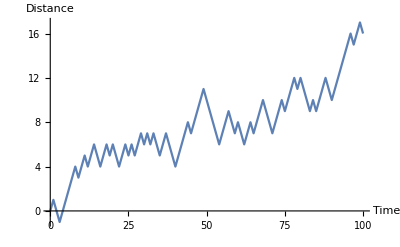

```mathematica
wanderingBug[p_]/;0≤p≤1:=RandomWalkProcess[p]
firstBug = wanderingBug[0.5];
firstBugPath=RandomFunction[RandomWalkProcess[0.5],{0,100}];
ListLinePlot[firstBugPath,AxesLabel->{"Time","Distance"}]
```

Let’s also visualize one hundred paths starting at 0 of the same sort of bug:

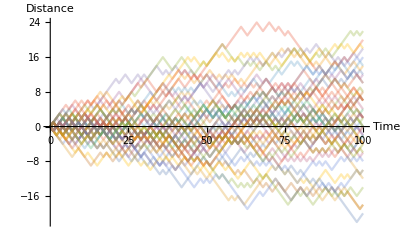

```mathematica
ListLinePlot[RandomFunction[firstBug,{0,100},50],PlotStyle->Opacity[0.3],AxesLabel->{"Time","Distance"}]
```

The bugs’ paths seem to spread out quite a bit around 0, but as a distribution they remain basically symmetrical about 0.

Let's check out how the distributions of paths evolve with changing p by using the Manipulate function:

```mathematica
Manipulate[ListLinePlot[RandomFunction[wanderingBug[p],{0,100},50],AxesLabel->{"Time","Distance"},PlotStyle->Opacity[0.3]],{{p,0.5,"p"},0,1,.1,Appearance->"Labeled"}]
```

As we ought to expect, as p increases the bug spends more time at positive distance from the origin. Interestingly, the spread of the paths tightens up as p gets further away from 0.5. We should definitely have expected this for p = 0 or 1, since this means the bug “almost always” walks backward or forward respectively. Can we argue for the nondegenerate case that this should happen? Sure, with some extra math.

There is a distribution called the BinomialDistribution[n,p] which is a discrete probability distribution which will tell you the probability of having k successes in a game with n trials of which the success probability is p. This relates to our bug by mapping “successes” onto “moves forward” and “failures” onto “moves backward;” hence, if we have k moves forward in t steps, the bug will have moved forward k times and backward t-k times for a total motion of 2k-t. Hence our distribution for the bug’s position at time t is

```mathematica
𝒟=TransformedDistribution[2k-t,k\[Distributed]BinomialDistribution[t,p]]
```

TransformedDistribution[2 x-t,x\[Distributed]BinomialDistribution[t,p]]

```mathematica
PDF[𝒟]
```

Function[x,Piecewise[{{(1-p)^(1/2 (-x-t)+t) p^((x+t)/2) Binomial[t,(x+t)/2], x+t≥0&&x-t≤0}, {0, True}}],Listable]

The conditional bit is a bit funky. Let’s plot just the nonconditional bit and see if it’s basically what we expect, handling by cases p=0 and p=1.

```mathematica
bugDist[p_][t_][x_]/;0≤p≤1:=Piecewise[({{(1-p)^(1/2 (-x-t)+t) p^((x+t)/2) Binomial[t, (x+t)/2], 0<p<1&&-t≤x≤t}, {KroneckerDelta[x,t], p==1}, {KroneckerDelta[x,-t], p==0}})]
```

```mathematica
steps=20;
Manipulate[DiscretePlot3D[bugDist[p][t][x],{t,0,steps},{x,-steps,steps},AxesLabel->{"Steps taken","Bug location","Probability"},ExtentSize->Full,ColorFunction->Hue],{{p,0.5,"p"},0,1,.1,Appearance->"Labeled"}]
```

This big Manipulate graphic won’t load very smoothly past about 20 steps taken, but we can still compare it with the paths of 50 bugs taking 20 steps, which we produce again here for convenience so you can compare with the probability distributions above:

```mathematica
Manipulate[ListLinePlot[RandomFunction[wanderingBug[p],{0,20},50],AxesLabel->{"Time","Distance"},PlotStyle->Opacity[0.3]],{{p,0.5,"p"},0,1,.1,Appearance->"Labeled"}]
```

Let’s also collect histograms on bug movement to check with our result: here’s a manipulatable histogram on the final positions of 500 bugs having taken 20 steps:

```mathematica
makeBugPaths[p_]:=RandomFunction[wanderingBug[p],{0,100},500]["PathFunction",All]
Manipulate[Histogram[#[20]&/@makeBugPaths[p],{-21,21,1}],{{p,0.5,"p"},0,1,.1,Appearance->"Labeled"}]
```

## Brownian Motion: Continuous-time Random Processes

Although the formal math required to prove it is somewhat involved, heuristically we can take a limit of the random walk in the continuum by “zooming out” from the lattice arbitrarily far. Instead of unit steps in time and distance, the separation between points become infinitesimal δt’s and δx’s and we can parameterize the plane by the coordinates (t,x). Random walks on this real-value-parameterized plane become Brownian Movers, or Wiener Processes.

This code produces some tracts of Brownian movers with drift μ  and volatility σ . These parameters control, respectively, the average progression of the mover and its deviation from the average progression.

```mathematica
Manipulate[ListLinePlot[RandomFunction[WienerProcess[μ,σ],{0,20,0.05},50],PlotStyle->Opacity[.2]],{μ,-2,2,0.1},{σ,0.01,2}]
```

Brownian movers are characterized by their time-slice probability distributions following Gaussians whose means and spread progress linearly in time:

```mathematica
WienerProcess[μ,σ][t]
```

NormalDistribution[t μ,√t σ]

We can visualize the evolution of the distribution as in the discrete case as follows:

```mathematica
Manipulate[Plot3D[PDF[WienerProcess[μ,σ][t],x],{t,1,20},{x,-20,20},PlotRange->{0,1},PerformanceGoal->"Quality",Mesh->None,ColorFunction->Hue],{{μ,0,"μ"},-2,2,.1,Appearance->"Labeled"},{{σ,0.5,"σ"},0.01,2,.1,Appearance->"Labeled"}]
```

## Stochastic Calculus

One of the reasons Wiener Processes are important is that they are the building blocks for a more general class of processes called Ito Processes which model many different phenomena. Smooth functions of Ito Processes may be Taylor-expanded, and the expansion allows us to turn a microscopic equation of a stochastically mobile object into a partial differential equation of its probability distribution. But let’s first start with some calculus.

Recall that one of the more arcane ways of defining a derivative is that f is differentiable at p with derivative a linear map Df(p) if

```mathematica
f(p+v)-f(p) = Df(p)·v + o(||v||)
```

In the stochastic world, we define similarly that X_t satisfies the stochastic differential equation (SDE)

```mathematica
ⅆ Subscript[X, t]=µ(t,Subscript[X, t]) ⅆt+σ(t,Subscript[X, t]) ⅆW
```

if for all t,

X_(t + h) − X_t − hµ(t, X_t) − σ(t, X_t)(W_(t + h) − W_t)

is a random variable with mean and variance going as o(h) and W_t a Wiener Process.

The important bit is that if X_t solves the SDE

ⅆX_t = µ(t)X_t ⅆt + σ(t)X_t ⅆW_t

then we call X_t an Ito Process. By Ito’s Lemma a two-argument twice-differentiable function f called on  (X_t,t) is an Ito Process satisfying

ⅆ(f(X_t,t)) = ∂_t f(X_t,t)ⅆt + ∂_x f(X_t,t)ⅆX_t +1∂_(x,x) f(X_t,t)ⅆX_t^2

where ⅆ X_t^2 is defined by the relations ⅆ t^2=0, ⅆtⅆ W_t=0, ⅆ W_t^2 = ⅆt. Above is the promised “taylor expansion,” whose higher order terms have all vanished on account of the relations in the preciding sentence.

This is all well and good, but can we calculate anything with it? Certainly. Let’s figure out the dynamics of a particle in a harmonic potential which is being buffeted by impacts of much less massive particles in a solution they are both immersed in. Suppose the buffeting is realized as a Gaussian noise term.

We write down Newton's second law; η is Gaussian noise:

```mathematica
m (∂^2 x(t))/(∂t^2)= -(∂V(x))/(∂x)+(∂η(t))/(∂t)
```

we rewrite this in terms of the momentum p = m dx/dt:

```mathematica
ⅆp= -V'(x)ⅆt + ⅆη
ⅆx = 1/m p ⅆt.
```

Now we leverage the Wolfram Language’s built-in support for Ito calculus to define precisely our problem

We can simply plug in the above two equations in differential form to ItoProcess. We define the particle immersed in liquid and trapped harmonically to the origin with mass 1 and spring constant 1, as well as a particle in the liquid with no confining potential. Initial positions and momenta are set to 0.

```mathematica
immersedParticle=ItoProcess[ⅆx[t]==p[t] ⅆt&&ⅆp[t]==-x[t]ⅆt+ⅆη[t],{x[t],p[t]},{{x,p},{0,0}},t,η\[Distributed]WienerProcess[]];
freeParticle=ItoProcess[ⅆx[t]==p[t] ⅆt&&ⅆp[t]==ⅆη[t],{x[t],p[t]},{{x,p},{0,0}},t,η\[Distributed]WienerProcess[]];
```

We plot an immersed, confined particle’s position and momentum both as functions of time and on a phase diagram.

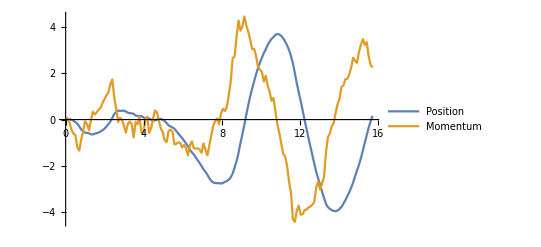

```mathematica
ListLinePlot[RandomFunction[immersedParticle,{0,5π,0.1}],PlotLegends->{"Position","Momentum"}]
```

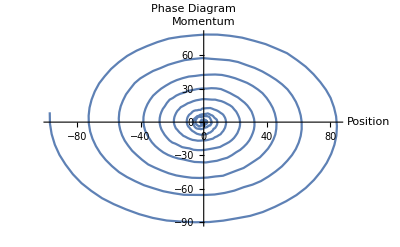

```mathematica
ListLinePlot[#["Values"]&/@Table[RandomFunction[immersedParticle,{0,20π,0.1}],{k,1,1}],PlotLabel->"Phase Diagram",AxesLabel->{"Position","Momentum"}]
```

We calculate the PDF and plot it; weirdly, we can’t just put “immersedPDF”into Plot3D directly and have it plot anything, even if we put an Evaluate around it. So I just copy/paste the result,which is quite lengthy. But we obtain the plots!

```mathematica
immersedPDF=PDF[SliceDistribution[immersedParticle,t],{x,p}];
freePDF=PDF[SliceDistribution[freeParticle,t],{x,p}];
```

```mathematica
Manipulate[Plot3D[ⅇ^(1/2 ((-4 (p^2 t-p x+t x^2+p x Cos[2 t])+2 (p-x) (p+x) Sin[2 t])/(-1+2 t^2+Cos[2 t])))/(2 π √(1/8 (-1+2 t^2+Cos[2 t]))),{p,-8,8},{x,-8,8},PlotRange->{0,.1},AxesLabel->Automatic,ColorFunction->Hue],{t,1,8}]
Manipulate[Plot3D[(√3 ⅇ^(1/2 (-(2 p (2 p t-3 x))/t^2+(6 (p t-2 x) x)/t^3)))/(π √(t^4)),{p,-8,8},{x,-8,8},PlotRange->{0,.1},AxesLabel->Automatic,ColorFunction->Hue],{t,1,8}]
```

As shown in the PDF’s of the phase diagrams, the trapped particle is confined by the harmonic potential to a 2D-gaussian-looking region with a circular cross section. This is reminiscent of the noiseless phase diagram, where the trajectories in phase space are all circles. The free noisy PDF has expected momentum around 0 but spreads out in space over time.

To calculate these PDF’s directly requires using Ito’s lemma to derive the Feynman-Kac equation, a PDE whose solution is the PDF of the problem above. But in nice enough scenarios, the Wolfram Language can complete the work for us.